```mathematica
S=Import["/home/artem/projects/solver/build/Solve/Solve2spectrum.txt", "table"];
S=Table[{3*10^10/S[[i,1]]*10^7,S[[i,2]]}, {i,2,Length[S]}];

S0=Import["/home/artem/projects/solver/build/Solve/noscat/Solve2spectrum.txt", "table"];
S0=Table[{3*10^10/S0[[i,1]]*10^7,S0[[i,2]]}, {i,2,Length[S]}];
```

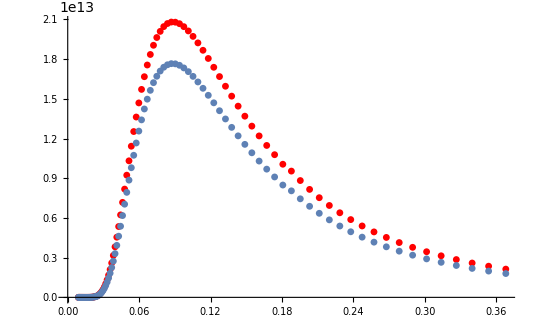

```mathematica
Show[
ListPlot[{Table[S[[i]],{i,300,400}]}, PlotStyle->Red],
ListPlot[{Table[S0[[i]],{i,300,400}]}]
]
```

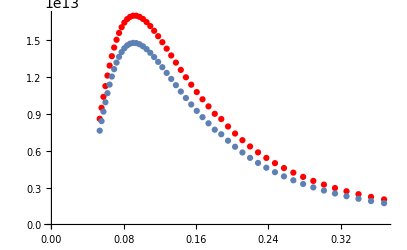

```mathematica
Show[
ListPlot[{Table[S[[i]],{i,300,350}]}, PlotStyle->Red],
ListPlot[{Table[S0[[i]],{i,300,350}]}]
]
```

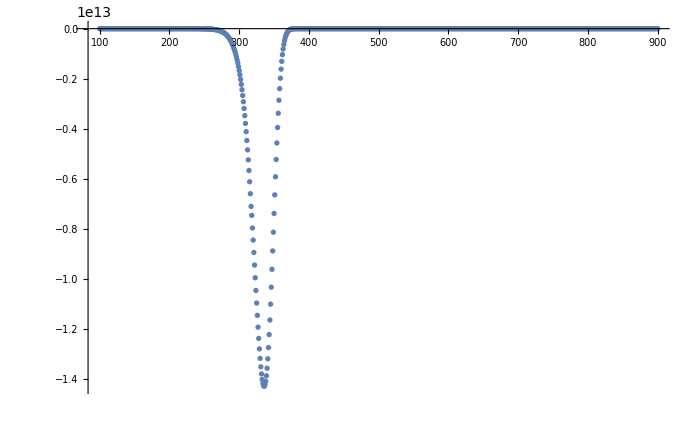

```mathematica
ListPlot[Table[{i,S[[i,2]]-S0[[i,2]]},{i,100,900}],PlotRange->All]
```

```mathematica
{S[[333]],(S[[338,2]]-S0[[338,2]])/S[[338,2]]}//N
```

{{0.101319,15.5593},0.594578}

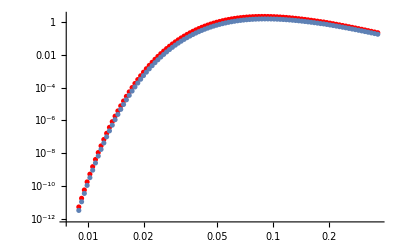

```mathematica
Show[
ListLogLogPlot[{Table[S[[i]],{i,300,400}]}, PlotStyle->Red],
ListLogLogPlot[{Table[S0[[i]],{i,300,400}]}]
]
```

```mathematica
kRelectron=2.8179403*10^-13;
cc=kRelectron^2*2*Pi;
eps=2/10^6;
eps21=2*eps+1;
lneps21=(Log[2*eps+1]/eps);
cc*(((1+eps)/(eps*eps))*(2*(1+eps)/(eps21)-lneps21)+lneps21/2-(1+3*eps)/(eps21*eps21))//N
```

7.33984×10^-24

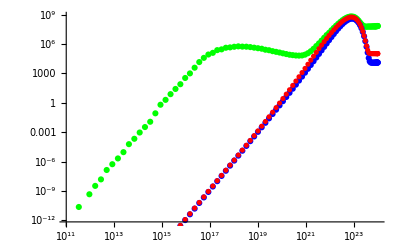

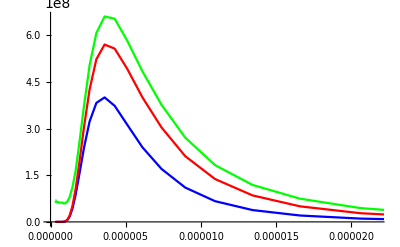

```mathematica
S=Import["/home/artem/projects/solver/build/Solve/Solve0spectrum.txt", "table"];
S1=Import["/home/artem/projects/solver/build/Solve/Solve1spectrum.txt", "table"];
S2=Import["/home/artem/projects/solver/build/Solve/Solve2spectrum.txt", "table"];
S=Table[{S[[i,1]],S[[i,2]]}, {i,2,Length[S]}];
S1=Table[{S1[[i,1]],S1[[i,2]]}, {i,2,Length[S]}];
S2=Table[{S2[[i,1]],S2[[i,2]]}, {i,2,Length[S]}];

Show[
ListLogLogPlot[S2, PlotStyle->Green],
ListLogLogPlot[S1, PlotStyle->Blue],
ListLogLogPlot[S, PlotStyle->Red]
]


S=Table[{3*10^10/S[[i,1]]*10^7,S[[i,2]]}, {i,1,Length[S]}];
S1=Table[{3*10^10/S1[[i,1]]*10^7,S1[[i,2]]}, {i,1,Length[S1]}];
S2=Table[{3*10^10/S2[[i,1]]*10^7,S2[[i,2]]}, {i,1,Length[S2]}];
Show[
ListLinePlot[{Table[S2[[i]],{i,60,95}]}, PlotStyle->Green],
ListLinePlot[{Table[S1[[i]],{i,60,95}]}, PlotStyle->Blue],
ListLinePlot[{Table[S[[i]],{i,60,95}]}, PlotStyle->Red]
]
```